```mathematica
NN = 1;
```

```mathematica
α = 4;
```

```mathematica
γ=4;
```

```mathematica
R0 = 2;
```

```mathematica
phiS[k_,s_,a_,b_]:=((1+b/a)^k/Beta[a,b])*NIntegrate[Exp[(1+b/a)*Log[Max[s,10^-12]]*x]*x^(k+a-1)*(1-x)^(b-1),{x,0,1}]
```

## Model equations

```mathematica
SEIRmodel[t_,s0_]:=NDSolve[{
s'[t]==-R0 * γ* s[t]*i[t],
e'[t]==R0 * γ* s[t]*i[t]-α*e[t],
i'[t]==α* e[t]-γ *i[t],
r'[t]==γ*i[t],
s[t/;t≤0]==s0,
e[t/;t≤0]==0.5*(1-s0),
i[t/;t≤0]==0.5*(1-s0),
r[t/;t≤0]==0
},{s[t],e[t],i[t],r[t]},{t,0,1000}];
```

```mathematica
SEIRHETmodel[t_,s0_,p_]:=NDSolve[{
s'[t]==-R0 * γ* s[t]^(1+1/p)*i[t],
e'[t]==R0 * γ* s[t]^(1+1/p)*i[t]-α*e[t],
i'[t]==α* e[t]-γ *i[t],
r'[t]==γ*i[t],
s[t/;t≤0]==s0,
e[t/;t≤0]==0.5*(1-s0),
i[t/;t≤0]==0.5*(1-s0),
r[t/;t≤0]==0
},{s[t],e[t],i[t],r[t]},{t,0,1000}];
SEIRHETmodelcorr[t_,s0_,p_]:=NDSolve[{
s'[t]==-R0 * γ* p/(p+1)* s[t]^(1+1/p)*v[t],
u'[t]==R0 *γ* s[t]^(1+2/p)*v[t]-α*u[t],
v'[t]==α*u[t]-γ*v[t],
e'[t]==R0 * γ* p/(p+1)* s[t]^(1+1/p)*v[t]-α*e[t],
i'[t]==α*e[t]-γ*i[t],
r'[t]==γ*i[t],
s[t/;t≤0]==s0,
e[t/;t≤0]==0.5*(1-s0),
u[t/;t≤0]==0.5*(1-s0),
v[t/;t≤0]==0.5*(1-s0),
i[t/;t≤0]==0.5*(1-s0),
r[t/;t≤0]==0
},{s[t],u[t],v[t],e[t],i[t],r[t]},{t,0,1000}];
```

```mathematica
SEIRHETmodelbeta[t_,s0_,a_,b_]:=NDSolve[{
s'[t]==-R0 * γ* s[t]*v[t],
u'[t]==R0 *γ* phiS[1, s[t], a, b]*v[t]-α*u[t],
v'[t]==α*u[t]-γ*v[t],
e'[t]==R0 * γ*  phiS[1, s[t], a, b]*v[t]-α*e[t],
i'[t]==α*e[t]-γ*i[t],
r'[t]==γ*i[t],
s[t/;t≤0]==s0,
e[t/;t≤0]==0.5*(1-s0),
u[t/;t≤0]==0.5*(1-s0),
v[t/;t≤0]==0.5*(1-s0),
i[t/;t≤0]==0.5*(1-s0),
r[t/;t≤0]==0
},{s[t],u[t],v[t],e[t],i[t],r[t]},{t,0,1000}];
```

```mathematica
SEIRHETmodelbetacorr[t_,s0_,a_,b_]:=NDSolve[{
s'[t]==-R0 * γ*(a*(a+b+1))/((a+b)*(a+1))* s[t]*v[t],
u'[t]==R0 *γ*(a*(a+b+1))/((a+b)*(a+1))* phiS[2, s[t], a, b]*v[t]-α*u[t],
v'[t]==α*u[t]-γ*v[t],
e'[t]==R0 * γ*(a*(a+b+1))/((a+b)*(a+1))*  phiS[1, s[t], a, b]*v[t]-α*e[t],
i'[t]==α*e[t]-γ*i[t],
r'[t]==γ*i[t],
s[t/;t≤0]==s0,
e[t/;t≤0]==0.5*(1-s0),
u[t/;t≤0]==0.5*(1-s0),
v[t/;t≤0]==0.5*(1-s0),
i[t/;t≤0]==0.5*(1-s0),
r[t/;t≤0]==0
},{s[t],u[t],v[t],e[t],i[t],r[t]},{t,0,1000}];
```

## Prevalence and final size curves

### Prevalence, k = 1

```mathematica
Plot[Evaluate[e[t]+i[t]/.{
SEIRmodel[t,0.998],
SEIRHETmodel[t,0.998,0.5],
SEIRHETmodel[t,0.998,1],
SEIRHETmodel[t,0.998,3],
SEIRHETmodelbeta[t,0.998,2,6],
SEIRHETmodelbeta[t,0.998,1,1],
SEIRHETmodelbeta[t,0.998,0.5,0.3]}],{t,0,10},
ImageSize->1000,
PlotStyle->{{ColorData["Crayola"]["Black"],AbsoluteThickness[0.5],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Thickness[0.0075]},{ColorData["Crayola"]["Blue"],Thickness[0.0075]},{ColorData["Crayola"]["SkyBlue"],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]}},AxesLabel -> {"time (days)", "Proportion of the pop."},AxesStyle->Directive[Black,FontSize->30],
PlotLegends->Placed[LineLegend[{"hom. SEIR","het. SEIR, p = 0.5", "het. SEIR, p = 1","het. SEIR, p = 3","het. SEIR, ϕ(x) ~ Beta(2, 6)", "het. SEIR, ϕ(x) ~ U(0, 2)","het. SEIR, ϕ(x) ~ Beta(0.5, 0.3)"(*, "3% tested daily", "4% tested daily"*)},Joined->False,LabelStyle->Directive[FontFamily->"Helvetica",Black,20],LegendMarkers->Graphics[{Thickness[1],Line[{{-20,0},{20,0}}]}]],{Right, Right}],BaseStyle->{FontSize->40,FontFamily->"Helvetica"},PlotRange->All]
```

NIntegrate::inumr: The integrand (1-x)^5 x^2 Max[1/1000000000000,s[t]]^(4 x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

### Final size, k = 1

```mathematica
Plot[Evaluate[r[t]/.{
SEIRmodel[t,0.998],
SEIRHETmodel[t,0.998,0.5],
SEIRHETmodel[t,0.998,1],
SEIRHETmodel[t,0.998,3],
SEIRHETmodelbeta[t,0.998,2,6],
SEIRHETmodelbeta[t,0.998,1,1],
SEIRHETmodelbeta[t,0.998,0.5,0.3]}],{t,0,10},
ImageSize->1000,
PlotStyle->{{ColorData["Crayola"]["Black"],AbsoluteThickness[0.5],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Thickness[0.0075]},{ColorData["Crayola"]["Blue"],Thickness[0.0075]},{ColorData["Crayola"]["SkyBlue"],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]}},AxesLabel -> {"time (days)", "Proportion of the pop."},AxesStyle->Directive[Black,FontSize->30],
PlotLegends->Placed[LineLegend[{"hom. SEIR","het. SEIR, p = 0.5", "het. SEIR, p = 1","het. SEIR, p = 3","het. SEIR, ϕ(x) ~ Beta(2, 6)", "het. SEIR, ϕ(x) ~ U(0, 2)","het. SEIR, ϕ(x) ~ Beta(0.5, 0.3)"(*, "3% tested daily", "4% tested daily"*)},Joined->False,LabelStyle->Directive[FontFamily->"Helvetica",Black,30],LegendMarkers->Graphics[{Thickness[1],Line[{{-20,0},{20,0}}]}]],{Right, Right}],BaseStyle->{FontSize->40,FontFamily->"Helvetica"},PlotRange->All]
```

NIntegrate::inumr: The integrand (1-x)^5 x^2 Max[1/1000000000000,s[t]]^(4 x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
LineLegend[{ColorData["Crayola"]["Black"],ColorData["Crayola"]["BlueViolet"],ColorData["Crayola"]["Blue"],ColorData["Crayola"]["SkyBlue"],{Dashed,ColorData["Crayola"]["BlueViolet"]},{Dashed,ColorData["Crayola"]["Blue"]},{Dashed,ColorData["Crayola"]["SkyBlue"]}},{"hom. SEIR","ϕ(x) ~ Gamma(0.5)", "ϕ(x) ~ Gamma(1)","ϕ(x) ~ Gamma(3)","ϕ(x) ~ Beta(2, 6)", " ϕ(x) ~ U(0, 2)","ϕ(x) ~ Beta(0.5, 0.3)"}, LegendLayout->{"Row",1}, LegendMarkerSize->40,LabelStyle->Directive[Bold, 18],LegendMarkers->Graphics[{Thickness[0.2],Line[{{-20,0},{20,0}}]}]]
```

### Prevalence, k = 2

NIntegrate::inumr: The integrand (1-x)^5 x^3 Max[1/1000000000000,s[t]]^(4 x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

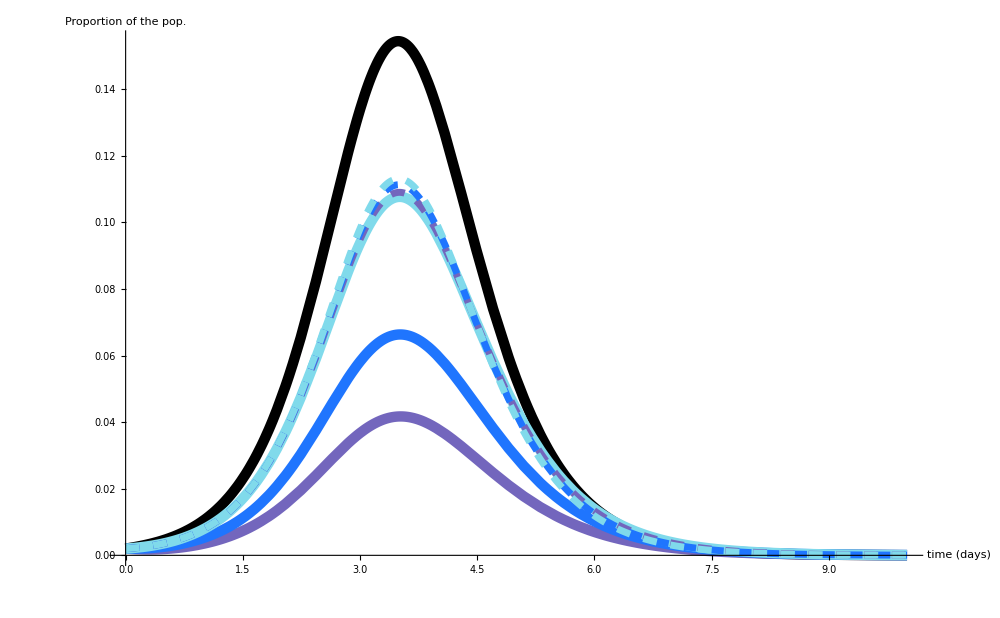

```mathematica
Plot[Evaluate[e[t]+i[t]/.{
SEIRmodel[t,0.998],
SEIRHETmodelcorr[t,0.998,0.5],
SEIRHETmodelcorr[t,0.998,1],
SEIRHETmodelcorr[t,0.998,3],
SEIRHETmodelbetacorr[t,0.998,2,6],
SEIRHETmodelbetacorr[t,0.998,1,1],
SEIRHETmodelbetacorr[t,0.998,0.5,0.3]}],{t,0,10},
ImageSize->1000,
PlotStyle->{{ColorData["Crayola"]["Black"],AbsoluteThickness[0.5],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Thickness[0.0075]},{ColorData["Crayola"]["Blue"],Thickness[0.0075]},{ColorData["Crayola"]["SkyBlue"],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]}},AxesLabel -> {"time (days)", "Proportion of the pop."},AxesStyle->Directive[Black,FontSize->30],
(*PlotLegends->Placed[LineLegend[{"hom. SEIR","het. SEIR (corr., p = 0.5)", "het. SEIR (corr., p = 1)","het. SEIR (corr., p = 3)","het. SEIR (corr., ϕ(x) ~ Beta(2, 6))", "het. SEIR (corr., ϕ(x) ~ U(0, 2))","het. SEIR (corr., ϕ(x) ~ Beta(0.5, 0.3))"(*, "3% tested daily", "4% tested daily"*)},Joined->False,LabelStyle->Directive[FontFamily->"Helvetica",Black,20],LegendMarkers->Graphics[{Thickness[1],Line[{{-20,0},{20,0}}]}]],{Right, Right}],BaseStyle->{FontSize->40,FontFamily->"Helvetica"},*)PlotRange->All]
```

### Final size, k = 2

NIntegrate::inumr: The integrand (1-x)^5 x^3 Max[1/1000000000000,s[t]]^(4 x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

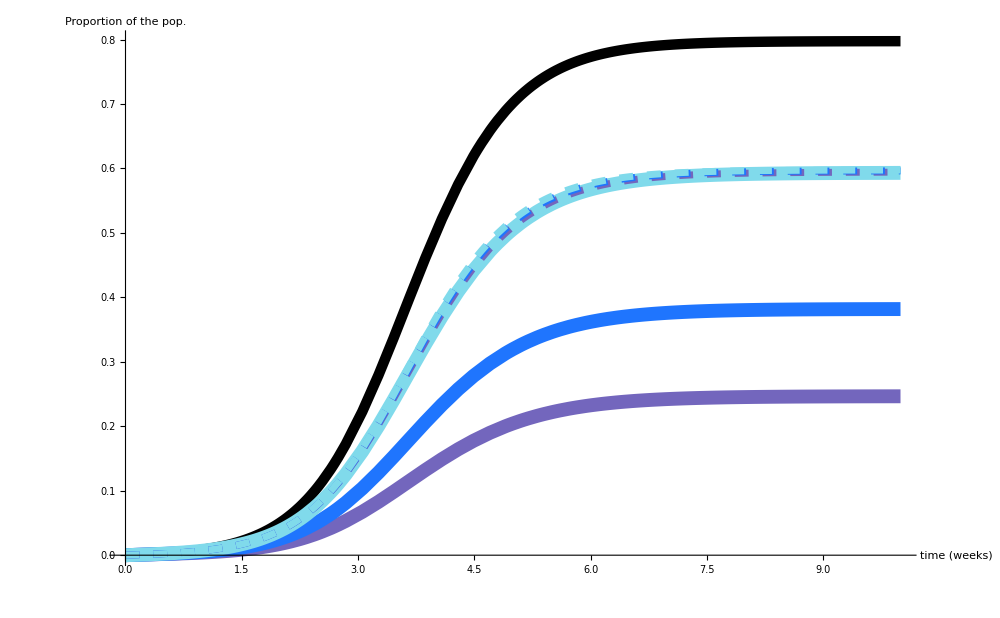

```mathematica
Plot[Evaluate[r[t]/.{
SEIRmodel[t,0.998],
SEIRHETmodelcorr[t,0.998,0.5],
SEIRHETmodelcorr[t,0.998,1],
SEIRHETmodelcorr[t,0.998,3],
SEIRHETmodelbetacorr[t,0.998,2,6],
SEIRHETmodelbetacorr[t,0.998,1,1],
SEIRHETmodelbetacorr[t,0.998,0.5,0.3]}],{t,0,10},
ImageSize->1000,
PlotStyle->{{ColorData["Crayola"]["Black"],AbsoluteThickness[0.5],Thickness[0.0075]},{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Thickness[0.01]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Orange"],Dashing[0.01],Thickness[0.005]}},AxesLabel -> {"time (weeks)", "Proportion of the pop."},AxesStyle->Directive[Gray,FontSize->20],
(*PlotLegends->Placed[LineLegend[{"hom. SEIR","het. SEIR (corr., p = 0.5)", "het. SEIR (corr., p = 1)","het. SEIR (corr., p = 3)","het. SEIR (corr., ϕ(x) ~ Beta(2, 6))", "het. SEIR (corr., ϕ(x) ~ U(0, 2))","het. SEIR (corr., ϕ(x) ~ Beta(0.5, 0.3))"(*, "3% tested daily", "4% tested daily"*)},Joined->False,LabelStyle->Directive[FontFamily->"Helvetica",Black,20],LegendMarkers->Graphics[{Thickness[1],Line[{{-20,0},{20,0}}]}]],{Right, Right}],BaseStyle->{FontSize->40,FontFamily->"Helvetica"},*)PlotRange->All]
```

```mathematica
LineLegend[{{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.03],Thickness[0.01]},,},{"ϕ(x) ~ Gamma(0.5)", "ϕ(x) ~ Gamma(1)","ϕ(x) ~ Gamma(3)"}, LegendLayout->{"Row",1}, LegendMarkerSize->40,LabelStyle->Directive[Bold, 18],LegendMarkers->Graphics[{Thickness[0.2],Line[{{-20,0},{20,0}}]}]]
```

```mathematica
LineLegend[{{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.03],Thickness[0.01]},,},{"ϕ(x) ~ Gamma(0.5)", "ϕ(x) ~ Gamma(1)","ϕ(x) ~ Gamma(3)"}, LegendLayout->{"Row",1}, LegendMarkerSize->40,LabelStyle->Directive[Bold, 18],LegendMarkers->Graphics[{Thickness[0.2],Line[{{-20,0},{20,0}}]}]]
```

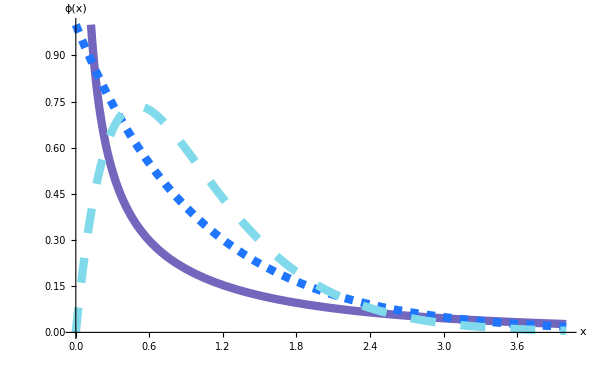

```mathematica
Plot[{PDF[GammaDistribution[1/3,3],x],PDF[GammaDistribution[1,1],x],PDF[GammaDistribution[2,0.5],x]},{x,0,4},PlotStyle->{{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.03,0.07],Thickness[0.01]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Orange"],Dashing[0.01],Thickness[0.005]}},BaseStyle->{FontSize->40,FontFamily->"Helvetica"},AxesLabel->{"x","ϕ(x)"},AxesStyle->Directive[Bold,Black, 22],PlotRange->{0,1}]
```

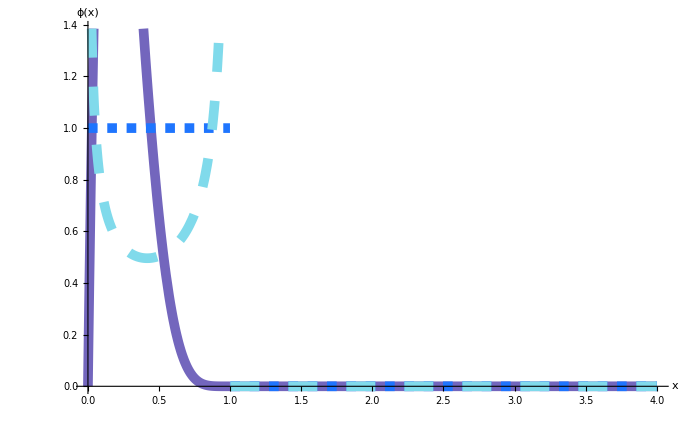

```mathematica
Plot[{PDF[BetaDistribution[2,6],x],PDF[BetaDistribution[1,1],x],PDF[BetaDistribution[0.5,0.3],x]},{x,0,4},PlotStyle->{{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.03,0.07],Thickness[0.01]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Orange"],Dashing[0.01],Thickness[0.005]}},BaseStyle->{FontSize->40,FontFamily->"Helvetica"},AxesLabel->{"x","ϕ(x)"},AxesStyle->Directive[Bold,Black, 22]]
```

```mathematica
extendedBeta[a_,b_,mean_,x_]:=1/(Beta[a,b]/Mean[BetaDistribution[a,b]])*(x/(1/Mean[BetaDistribution[a,b]]))^(a-1)*(1-x/(1/Mean[BetaDistribution[a,b]]))^(b-1)
```

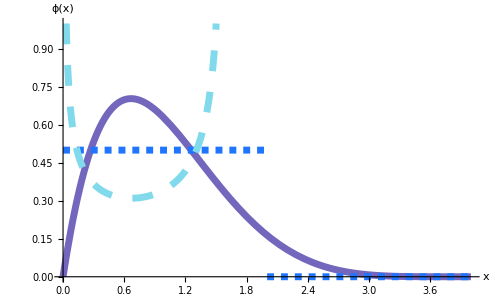

```mathematica
Plot[{extendedBeta[2,6,1,x],
PDF[UniformDistribution[{0,2}],x],
extendedBeta[0.5,0.3,1,x]},{x,0,4},PlotStyle->{{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.03,0.07],Thickness[0.01]},{ColorData["Crayola"]["BlueViolet"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.01],Thickness[0.005]},{ColorData["Crayola"]["Orange"],Dashing[0.01],Thickness[0.005]}},BaseStyle->{FontSize->40,FontFamily->"Helvetica"},AxesLabel->{"x","ϕ(x)"},AxesStyle->Directive[Bold,Black, 22],PlotRange->{0,1}]
```

```mathematica
Ű
```

```mathematica
LineLegend[{{ColorData["Crayola"]["BlueViolet"],Thickness[0.01]},{ColorData["Crayola"]["Blue"],Dashing[0.01],Thickness[0.01]},{ColorData["Crayola"]["SkyBlue"],Dashing[0.03],Thickness[0.01]},,},{"ϕ(x) ~ Beta(2, 6)", "ϕ(x) ~  Beta(1, 1)","ϕ(x) ~ Beta(0.5, 0.3)"}, LegendLayout->{"Row",1}, LegendMarkerSize->40,LabelStyle->Directive[Bold, 18],LegendMarkers->Graphics[{Thickness[0.2],Line[{{-20,0},{20,0}}]}]]
```